```mathematica
Moff[r_,R_,β_]:=(β-1)/(Pi R^2(1 + (r/R)^2)^β)
```

```mathematica
NIntegrate[2 Pi r Moff[r,1.2345,3.5567],{r,0,Infinity}]
```

1.

```mathematica
FindRoot[Moff[r, 1.,3.5] == Moff[0., 1.,3.5]/2, {r, .5}] (* find HWHM *)
```

{r→0.467989}

```mathematica
Integrate[2 Pi r r^2Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>2]
```

1/(-2+β)

```mathematica
Integrate[2 Pi r r^4Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>2]
```

If[Re[β]>3,2/(6-5 β+β^2),Integrate[-2 r^5 (1+r^2)^-β+2 r^5 (1+r^2)^-β β,{r,0,∞},Assumptions→2<Re[β]≤3]]

```mathematica
MoffM2[r_,RM_,β_]:=(β-1)/(Pi (β-2)RM^2(1 + (r/RM)^2/(β-2))^β)
```

```mathematica
(* so now M2 = RM^2 always *)
```

```mathematica
NIntegrate[2 Pi r r^2MoffM2[r,1.2345,3.5678]/1.2345^2,{r,0,Infinity}]
```

1.

```mathematica
MoffM2[0,RM,β]
```

(-1+β)/(π RM^2 (-2+β))

```mathematica
FindRoot[MoffM2[r, 1.,3.5] == MoffM2[0., 1.,3.5]/2, {r, .5}] (* find HWHM *)
```

{r→0.573167}

```mathematica
1/0.5731670623009607
```

1.74469

```mathematica
(* so HWHM is 0.573167 R  *)
```

```mathematica
Moff35h[r_,Rhwhm_]:=5 0.4679889466691232^2/(2Pi)/Rhwhm^2 (1 + (0.4679889466691232r/Rhwhm)^2)^(-3.5)
```

```mathematica
Moff35h[1,1]/ Moff35h[0,1]
```

0.5

```mathematica
FindRoot[Integrate[2 Pi r r^2 Moff35h[r,1],{r,0,Ref}]==0.5,{Ref,1}]
```

{Ref→1.44585}

```mathematica
MM2 =Integrate[2 Pi r r^2 Moff35h[r,1],{r,0,Infinity}]
```

3.04395

```mathematica
MM4=Integrate[2 Pi r r^4 Moff35h[r,1],{r,0,Infinity}]
```

55.5938

```mathematica
(* So the 2nd and 4th moments of Moff35[r,Rhwhm] are 3.044 Rhwhm^2 and 55.594 Rhwhm^4 *)
```

```mathematica
FindRoot[(1+r) Exp[-r]==0.5,{r,1}]
```

{r→1.67835}

```mathematica
ae=1.6783469900166608
```

1.67835

```mathematica
Integrate[ae^2r  Exp[-ae r],{r,0,1}]
```

0.5

```mathematica
EProf[r_,Re50_]:=1/(2Pi) (ae/Re50)^2Exp[-ae r/ Re50]
```

```mathematica
Integrate[2 Pi r EProf[r,1],{r,0,Infinity}]
```

1.

```mathematica
FindRoot[Integrate[2 Pi r  EProf[r,1],{r,0,Ref}]==0.5,{Ref,1}]
```

{Ref→1.}

```mathematica
FindRoot[EProf[Rhm,1]/EProf[0,1]==.5,{Rhm,1}]
```

{Rhm→0.412994}

```mathematica
ME2=Integrate[2 Pi r r^2 EProf[r,1],{r,0,Infinity}]
```

2.13004

```mathematica
ME4 =Integrate[2 Pi r  r^4 EProf[r,1],{r,0,Infinity}]
```

15.1236

```mathematica
(* So the 2nd and 4th moments of EProf[r,Ref] are 2.13004Ref^2 and 15.1235 Ref^4 *)
```

```mathematica
GProf[r_,Rrms_]:=1/(Pi Rrms^2  Exp[(r/Rrms)^2])
```

```mathematica
Integrate[2 Pi r GProf[r,1.2345],{r,0,Infinity}]
```

1.

```mathematica
FindRoot[Integrate[2 Pi r GProf[r,1],{r,0,Reff}]==.5,{Reff,1}]
```

{Reff→0.832555}

```mathematica
FindRoot[GProf[rhwhm,1]==GProf[0,1]/2,{rhwhm,1}]
```

{rhwhm→0.832555}

```mathematica
Sqrt[Integrate[2 Pi r r^2GProf[r,1.2345],{r,0,Infinity}]]
```

1.2345

```mathematica
MG2=Integrate[2 Pi r r^2GProf[r,1],{r,0,Infinity}]
```

1

```mathematica
MG4=Integrate[2 Pi r r^4GProf[r,1],{r,0,Infinity}]
```

2

```mathematica
MMEG2[Rhwhm_,Ref_,Rrms_]:= MM2 Rhwhm^2 + ME2 Ref^2 + MG2 Rrms^2
```

```mathematica
MMEG4[Rhwhm_,Ref_,Rrms_]:= MM4 Rhwhm^4 + ME4 Ref^4 + MG4 Rrms^4 + 4(MM2 Rhwhm^2 ME2 Ref^2 + MG2 Rrms^2MM2 Rhwhm^2 + ME2 Ref^2  MG2 Rrms^2)
```

```mathematica
Kurt[Rhwhm_,Ref_,Rrms_]:=MMEG4[Rhwhm,Ref,Rrms]/MMEG2[Rhwhm,Ref,Rrms]^2
```

```mathematica
Integrate[2 Pi r r ^2 Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>3]
```

1/(-2+β)

```mathematica
Integrate[2 Pi r  r^4Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>3]/Integrate[2 Pi r r ^2 Moff[r,1,β],{r,0,Infinity},Assumptions->Re[β]>3]^2
```

(2 (-2+β)^2 (-1+β) Gamma[-3+β])/Gamma[β]

```mathematica
KBeta[β_]:= (2 (-2+β)^2 (-1+β) Gamma[-3+β])/Gamma[β]
```

```mathematica
KBeta[{3.5,4,4.5,5}]
```

{6.,4,3.33333,3}

```mathematica
KBeta[β_]:= 2 (β-2)/(β-3)
```

```mathematica
KBeta[{3.5,4,4.5,5}]
```

{6.,4,3.33333,3}

```mathematica
BetaK[K_]:=(3K-4)/(K-2)
```

```mathematica
BetaK[{6.,4,3.333333333333333,3}]
```

{3.5,4,4.5,5}

```mathematica
BMEG[Rhwhm_,Ref_,Rrms_]:=(3Kurt[Rhwhm,Ref,Rrms]-4)/(Kurt[Rhwhm,Ref,Rrms]-2)
```

```mathematica
RMEG[Rhwhm_,Ref_,Rrms_]:=Sqrt[(BMEG[Rhwhm,Ref,Rrms]-2)MMEG2[Rhwhm,Ref,Rrms]]
```

```mathematica
BMEG[1,.5,0.5]
```

3.78213

```mathematica
BMEG[1,1,1]
```

4.76833

```mathematica
RMEG[1,0,0]
```

2.1368

```mathematica
RMEG[1,0.5,0.5]
```

2.61137

```mathematica
MEG0[Rhwhm_,Ref_,Rrms_]:=NIntegrate[2Pi r Moff[Sqrt[r^2+rt^2-2 r rt Cos[th]],RMEG[1,0,0]Rhwhm ,3.5]2  rt GProf[rt,Rrms]EProf[r,Ref],{th,0, Pi},{rt,0,3Rrms},{r,0,5Ref},AccuracyGoal->3]
```

```mathematica
MEG0[1,.5,.5]
```

0.11627

```mathematica
BetaMEG0[Rhwhm_,Ref_,Rrms_]:=If[Ref==0,(2 Pi MG0[Rhwhm,Rrms]MMEG2[Rhwhm,Ref,Rrms]-1)/( Pi MG0[Rhwhm,Rrms]MMEG2[Rhwhm,Ref,Rrms]-1),If[Rrms==0,(2 Pi ME0[Rhwhm,Ref]MMEG2[Rhwhm,Ref,Rrms]-1)/( Pi ME0[Rhwhm,Ref]MMEG2[Rhwhm,Ref,Rrms]-1),(2 Pi MEG0[Rhwhm,Ref,Rrms]MMEG2[Rhwhm,Ref,Rrms]-1)/( Pi MEG0[Rhwhm,Ref,Rrms]MMEG2[Rhwhm,Ref,Rrms]-1)]]
```

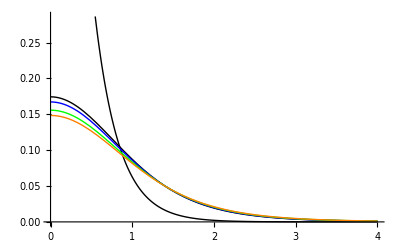

```mathematica
Plot[{Moff35h[r,1],
EProf[r,.5],
MEProf[r,1,.5],
Moff35h[r,Sqrt[1+(0.5 0.4129939664938205)^2]],
Moff35h[r,Sqrt[(1.4458473030317134^2+0.5^2)]/1.4458473030317134],
MoffM2[r,Sqrt[MMEG2[1,0.5,0]],3.5]},
{r,0,4},PlotStyle->{Black,Black,Red,Blue,Green,Orange,Purple}]
```

Plot::exclul: {0.279606\ Im[r^2/-2 + Times[« 2 »]] - 0} must be a list of equalities or real-valued functions.

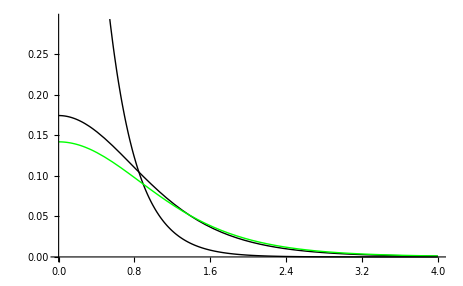

```mathematica
Plot[{Moff35h[r,1],
EProf[r,.5],
MEProf[r,1,.5],
MoffM2[r,Sqrt[MMEG2[1,0.5,0]],BetaMEG0[1,.5,0]],
Moff[r,RMEG[1,0.5,0],BMEG[1,.5,0]]},{r,0,4},PlotStyle->{Black,Black,Red,Blue,Green,Orange,Purple}]
```

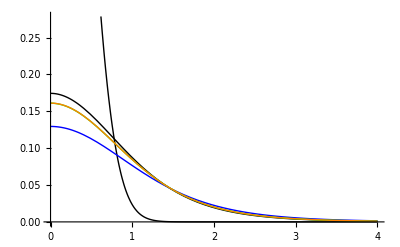

```mathematica
Plot[{Moff35h[r,1],
GProf[r,.5],
MGProf[r,1,.5],
Moff35h[r,Sqrt[1+0.5 0.8325546111576978^2]],
Moff35h[r,Sqrt[(1.4458473030317134^2+(0.8325546111576978 0.5)^2)]/1.4458473030317134],
MoffM2[r,Sqrt[MMEG2[1,0,0.5]],3.5]},{r,0,4},PlotStyle->{Black,Black,Red,Blue,Green,Orange,Purple}]
```

Plot::exclul: {0.303587\ Im[r^2/-2 + Times[« 2 »]] - 0} must be a list of equalities or real-valued functions.

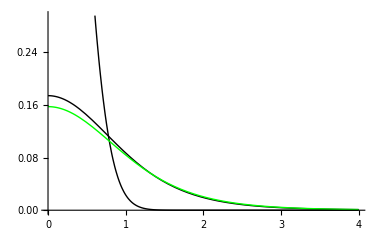

```mathematica
Plot[{Moff35h[r,1],
GProf[r,.5],
MGProf[r,1,.5],
MoffM2[r,Sqrt[MMEG2[1,0,0.5]],BetaMEG0[1,0,.5]],
Moff[r,RMEG[1,0,.5],BMEG[1,0,.5]]},{r,0,4},PlotStyle->{Black,Black,Red,Blue,Green,Orange,Purple}]
```

```mathematica
Moff[0,RMEG[1,0,0],3.5]
```

0.174286

```mathematica
NIntegrate[2 Pi r Moff[r,RMEG[1,0.5,0.5],BMEG[1,.5,0.5]],{r,0,Infinity}]
```

1.

```mathematica
MGProf[r_,Rhwhm_,Rrms_]:=NIntegrate[Moff[Sqrt[r^2+rt^2-2 r rt Cos[th]],RMEG[1,0,0]Rhwhm ,3.5]2  rt GProf[rt,Rrms],{th,0, Pi},{rt,0,3Rrms},AccuracyGoal->3]
```

```mathematica
MG0[Rhwhm_,Rrms_]:=NIntegrate[2 Pi r Moff[r,RMEG[1,0,0]Rhwhm ,3.5] GProf[r,Rrms],{r,0,3Rrms},AccuracyGoal->3]
```

```mathematica
MG0[1,.5]
```

0.147264

```mathematica
(2 Pi MG0[1,.5]MMEG2[1,0,0.5]-1)/( Pi MG0[1,.5]MMEG2[1,0,0.5]-1)
```

3.90866

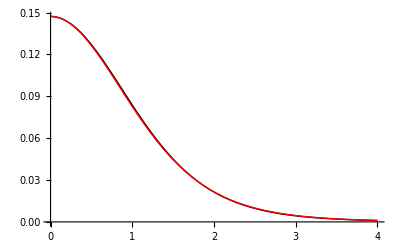

```mathematica
Plot[{MGProf[r,1,.5],MoffM2[r,Sqrt[MMEG2[1,0,0.5]],3.908656383171676]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
MEProf[r_,Rhwhm_,Ref_]:=NIntegrate[Moff[Sqrt[r^2+rt^2-2 r rt Cos[th]],RMEG[1,0,0]Rhwhm ,3.5]2  rt EProf[rt,Ref],{th,0, Pi},{rt,0,5Ref},AccuracyGoal->3]
```

```mathematica
ME0[Rhwhm_,Ref_]:=NIntegrate[2 Pi r Moff[r,RMEG[1,0,0]Rhwhm ,3.5] EProf[r,Ref],{r,0,5Ref},AccuracyGoal->3]
```

```mathematica
ME0[1,.5]
```

0.131901

```mathematica
MEProf[0,1,.5]
```

0.131903

```mathematica
(2 Pi ME0[1,.5]MMEG2[1,0.5,0]-1)/( Pi ME0[1,.5]MMEG2[1,0.5,0]-1)
```

4.07465

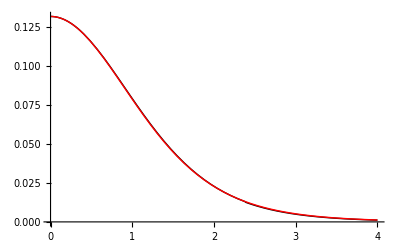

```mathematica
Plot[{MEProf[r,1,.5],MoffM2[r,Sqrt[MMEG2[1,0.5,0]],4.074645205109686]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

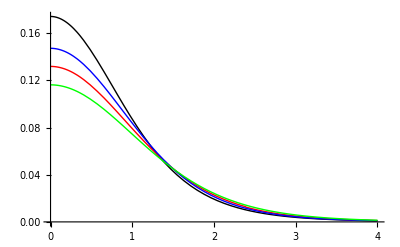

```mathematica
Plot[{Moff35h[r,1],MEProf[r,1,.5],MGProf[r,1,.5],MoffM2[r,Sqrt[MMEG2[1,0.5,0.5]],BetaMEG0[1,.5,.5]]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

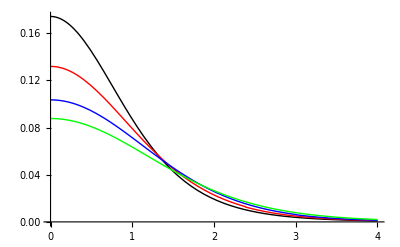

```mathematica
Plot[{Moff35h[r,1],MEProf[r,1,.5],MGProf[r,1,1],MoffM2[r,Sqrt[MMEG2[1,0.5,1]],(2 Pi MEG0[1,.5,1]MMEG2[1,0.5,1]-1)/( Pi MEG0[1,.5,1]MMEG2[1,0.5,1]-1)]},{r,0,4},PlotStyle->{Black,Red,Blue,Green}]
```

```mathematica
(*  start aperture stuff   *)
```

```mathematica
FWHMsee500=0.75
```

0.75

```mathematica
Rsee[λ_,AM_]:=FWHMsee500/2   (λ/500)^-0.2  AM^(3/5)
(* CTIO 0.75" median seeing at any Air Mass *)
```

```mathematica
Rgal=0.29
(* nominal ELG reff val at i=23.5, SK's formula *)
```

0.29

```mathematica
Rgalmax=0.41 (* Steve's cut *)
```

0.41

```mathematica
Rrmsfix=Sqrt[16.5^2 - 9.3^2]
```

13.6294

```mathematica
ApEff[Rseehm_,Rg_,Rrmstot_,Rapp_]:=NIntegrate[2 Pi r MoffM2[r,Sqrt[MMEG2[Rseehm,Rg,Rrmstot/56.73]],BetaMEG0[Rseehm,Rg,Rrmstot/56.73]],{r,0,Rapp}]
```

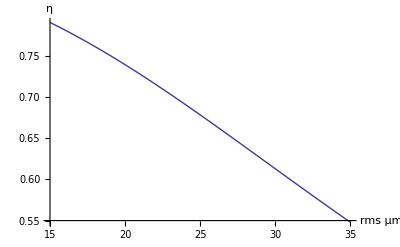

```mathematica
Plot[ApEff[0.3,0,Rrmstot,0.7],{Rrmstot,15,35},PlotStyle->Thick,AxesLabel-> {rms (μm),η},AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
ApEffvsrms[rms_]:=NIntegrate[2 Pi r MoffM2[r,Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+rms^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+rms^2]/56.73]],{r,0,1.8/2}]
```

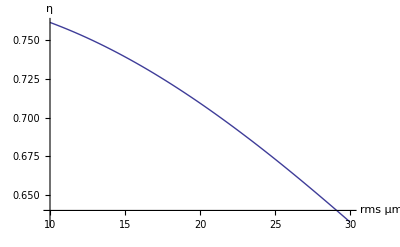

-Graphics-

```mathematica
Plot[ApEffvsrms[rms],{rms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),η},AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
AMloss[λ_]:=Switch[λ,
350,0.595,
370,0.614,
400,0.679,
450,0.770,
500,0.824,
550,0.846,
600,0.855,
650,0.883,
700,0.917,
750,0.943,
800,0.963,
850,0.976,
900,0.985,
950,0.991,
1000,0.993]
```

```mathematica
SNrms[λ_,dfib_,Rg_,AM_,Rrms_]:=AMloss[λ]^AM NIntegrate[ 2  Pi r MoffM2[r,Sqrt[MMEG2[Rsee[λ,AM],Rg,Sqrt[Rrmsfix^2+Rrms^2]/56.73]],BetaMEG0[Rsee[λ,AM],Rg,Sqrt[Rrmsfix^2+Rrms^2]/56.73]],{r,0,dfib/2}]/(Sqrt[AM] dfib)                  (* S/N ratio, assumes sky-limited *)
```

```mathematica
SNrms[850,1.8,Rgal,1.0,15]
```

0.400831

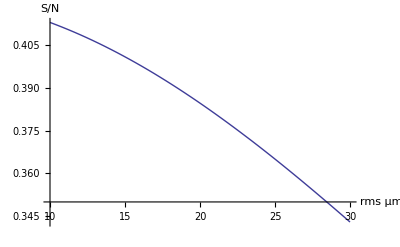

```mathematica
Plot[SNrms[850,1.8,Rgal,1.0,Rrms],{Rrms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),"S/N"},AxesStyle->Directive[Thick,14, Bold]]
```

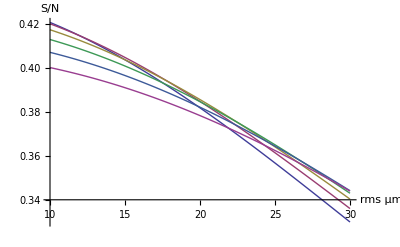

```mathematica
Plot[{SNrms[850,1.5,Rgal,1.0,Rrms],SNrms[850,1.6,Rgal,1.0,Rrms],SNrms[850,1.7,Rgal,1.0,Rrms],SNrms[850,1.8,Rgal,1.0,Rrms],SNrms[850,1.9,Rgal,1.0,Rrms],SNrms[850,2.0,Rgal,1.0,Rrms]},{Rrms,10,30},PlotStyle->Thick,AxesLabel->  {rms (μm),"S/N"},AxesStyle->Directive[Thick,14, Bold]]
```

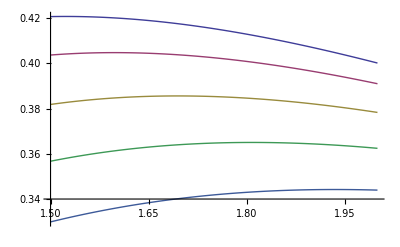

```mathematica
Plot[{SNrms[850,dfib,Rgal,1.0,10],SNrms[850,dfib,Rgal,1.0,15],SNrms[850,dfib,Rgal,1.0,20],SNrms[850,dfib,Rgal,1.0,25],SNrms[850,dfib,Rgal,1.0,30]},{dfib,1.5,2}]
```

```mathematica
RMSSpot3[λ_]=Switch[λ,370,75,400,61,450,45,500,30,
550,24,600,22,650,21,700,22,750,24,800,26,850,28,900,30,950,31,1000,33]
```

Switch[λ,
370,75,
400,61,
450,45,
500,30,
550,24,
600,22,
650,21,
700,22,
750,24,
800,26,
850,28,
900,30,
950,31,
1000,33]

```mathematica
Ropt3[λ_]:=Sqrt[(Rrmsfix^2+RMSSpot3[λ]^2)]/56.73
(* Rrms in arcsec, includes rms=Rrmsfixum for surface and alignment errors *)
```

```mathematica
Ropt3[650]
```

0.441304

```mathematica
SN3[λ_,dfib_,Rg_,AM_]:=NIntegrate[ 2  Pi r MoffM2[r,Sqrt[MMEG2[Rsee[λ,AM],Rg,Ropt3[λ]]],BetaMEG0[Rsee[λ,AM],Rg,Ropt3[λ]]],{r,0,dfib/2}]/dfib (* S/N ratio, assumes sky-limited *)
```

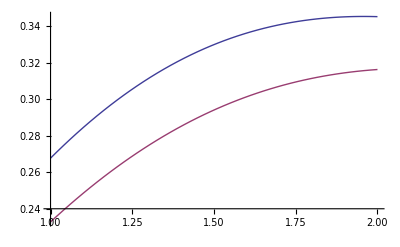

```mathematica
P38501=Plot[{SN3[850,dfib,Rgal,1.2],SN3[850,dfib,Rgalmax,1.2]},{dfib,1.0,2.0}]
```

```mathematica
RMSSpot7[λ_]=Switch[λ,
350,25.8,
370,24.7,
400,23.0,
450,19.9,
500,15.7,
550,13.3,
600,13.4,
650,13.4,
700,13.7,
750,14.1,
800,14.4,
850,15.3,
900,15.9,
950,16.6,
1000,17.3,
1050,18.1]
```

Switch[λ,
350,25.8,
370,24.7,
400,23.,
450,19.9,
500,15.7,
550,13.3,
600,13.4,
650,13.4,
700,13.7,
750,14.1,
800,14.4,
850,15.3,
900,15.9,
950,16.6,
1000,17.3,
1050,18.1]

```mathematica
Ropt7[λ_]:=Sqrt[(Rrmsfix^2+RMSSpot7[λ]^2)]/56.73
(* Rrms in arcsec, includes rms=Rrmsfixum for surface and alignment errors *)
```

```mathematica
SN7[λ_,dfib_,Rg_,AM_]:=NIntegrate[ 2  Pi r MoffM2[r,Sqrt[MMEG2[Rsee[λ,AM],Rg,Ropt7[λ]]],BetaMEG0[Rsee[λ,AM],Rg,Ropt7[λ]]],{r,0,dfib/2}]/dfib (* S/N ratio, assumes sky-limited *)
```

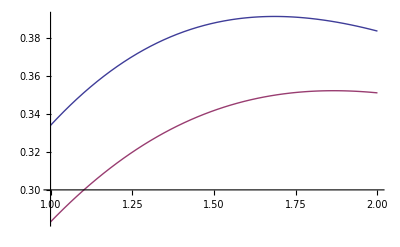

```mathematica
P7850g=Plot[{SN7[850,dfib,Rgal,1.2],SN7[850,dfib,Rgalmax,1.2]},{dfib,1.0,2.0}]
```

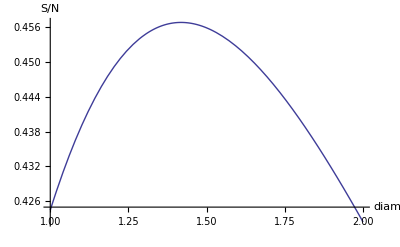

```mathematica
P7850s=Plot[SN7[850,dfib,0,1.2],{dfib,1.0,2.0},PlotStyle->Thick,AxesLabel->  {diam,"S/N"},AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
Frac[r1_,r2_,del_]:=If[del==0,0,Re[ArcCos[Max[-1,Min[1,(r1^2+del^2-r2^2 )/(2r1 Abs[del])]]]/Pi]]
```

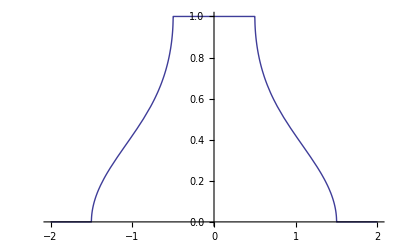

```mathematica
Plot[Frac[0.5,1,del],{del,-2,2}]
```

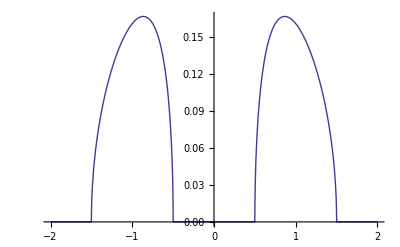

```mathematica
Plot[Frac[1,0.5,del],{del,-2,2}]
```

```mathematica
Frac[1,1,1]
```

1/3

```mathematica
AppEffd[R_,β_,rapp_,del_]:=If[del==0,NIntegrate[2 Pi r MoffM2[r,R,β],{r,0,rapp}],NIntegrate[2 Pi r Frac[r,rapp,del]MoffM2[r,R,β],{r,0,Infinity}]]
```

```mathematica
AppEffd[1,3.5,1,0]
```

0.721145

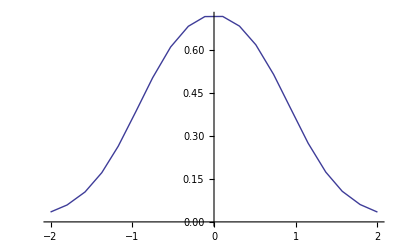

```mathematica
Plot[AppEffd[1,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

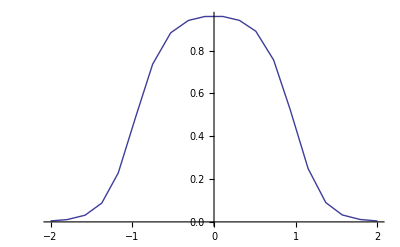

```mathematica
Plot[AppEffd[.5,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

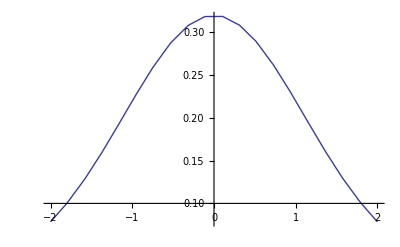

```mathematica
Plot[AppEffd[2,3.5,1,del],{del,-2,2},PlotPoints->20,MaxRecursion->0]
```

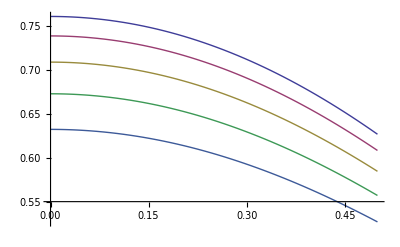

```mathematica
Plot[{AppEffd[Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+10^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+10^2]/56.73],1.8/2,del],AppEffd[Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+15^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+15^2]/56.73],1.8/2,del],AppEffd[Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+20^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+20^2]/56.73],1.8/2,del],AppEffd[Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+25^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+25^2]/56.73],1.8/2,del],AppEffd[Sqrt[MMEG2[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+30^2]/56.73]],BetaMEG0[Rsee[850,1],Rgal,Sqrt[Rrmsfix^2+30^2]/56.73],1.8/2,del]},{del,0,0.5}]
```

```mathematica
SN7d[λ_,dfib_,Rg_,AM_,del_]:=
AppEffd[Sqrt[MMEG2[Rsee[λ,AM],Rg,Ropt7[λ]]],BetaMEG0[Rsee[λ,AM],Rg,Ropt7[λ]],dfib/2,del]/dfib (* S/N ratio, assumes sky-limited *)
```

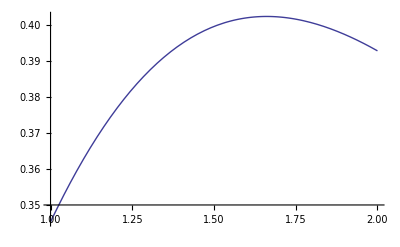

```mathematica
P7850Zg=Plot[SN7d[850,dfib,Rgal,1.0,10/56.73],{dfib,1.0,2.0}]
```

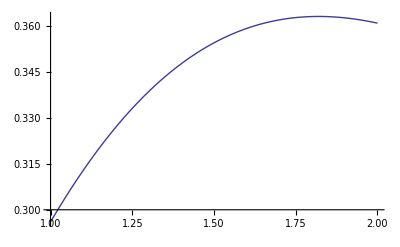

```mathematica
P785014g=Plot[SN7d[850,dfib,Rgal,1.4,10/56.73],{dfib,1.0,2.0}]
```

```mathematica
(* T=11.5 C,RH=44.2%,P=772.2mbar *)
```

```mathematica
ZD[AM_]:=ArcCos[1/AM]
```

```mathematica
TC=11.5
```

11.5

```mathematica
T=273.16+TC
```

284.66

```mathematica
PS=-10474.0+116.43 T-0.43284 T^2+0.00053840 T^3
```

14.3051

```mathematica
RH=.442
```

0.442

```mathematica
P2=RH PS
```

6.32284

```mathematica
P1=772.2
```

772.2

```mathematica
D1=P1/T (1.0+P1 (57.90  10^-8-(9.3250 10^-4/T)+(0.25844/T^2)))
```

2.71374

```mathematica
D2=P2/T(1.0+P2 (1.0+3.7 10^-4P2)(-2.37321 10^-3+(2.23366/T)-(710.792/T^2)+(7.75141 10^4/T^3)))
```

0.0222207

```mathematica
N1[λ_]:=1.0 10^-8((2371.34+683939.7/(130-1/λ^2)+4547.3/(38.9-1/λ^2)) D1+ (6487.31+58.058/λ^2-0.71150/λ^4+0.08851/λ^6) D2)
```

```mathematica
N1[.5]
```

0.000216684

```mathematica
DR[λ_,λ0_,AM_]:=Tan[ZD[AM]](N1[λ0/1000]-N1[λ/1000]) 206264.8
```

```mathematica
DR[600,500,1.1]
```

0.146518

```mathematica
DR[350,400,1.2]
```

-0.358024

```mathematica
ADCloss[λ_]:=Switch[λ,
350,0.78,
370,.863,
400,.941,
450,.935,
500,.931,
550,.936,
600,.942,
650,.946,
700,.957,
750,.962,
800,.966,
850,.963,
900,.959,
950,.955,
1000,.951,
1050,0.947] (* last number 0.947 estimated*)
```

```mathematica
AMloss[λ_]:=Switch[λ,
350,0.595,
370,0.614,
400,0.679,
450,0.770,
500,0.824,
550,0.846,
600,0.855,
650,0.883,
700,0.917,
750,0.943,
800,0.963,
850,0.976,
900,0.985,
950,0.991,
1000,0.993]
```

```mathematica
FAM[AM_]:=Switch[AM,
1.05,0.333,
1.15,0.314,
1.25,0.224,
1.35,0.09,
1.45,0.024,
1.55,0.01,
1.65,0.001,
1.75,0.001,
1.85,0.001,
1.95,0,
2.05,0]  (* deleted 2.05 field, special request! *)
```

```mathematica
AppEffDR7[λ_,λ0_,AM_,rapp_,Rg_]:=AppEffd[Sqrt[MMEG2[Rsee[λ,AM],Rg,Ropt7[λ]]],BetaMEG0[Rsee[λ,AM],Rg,Ropt7[λ]],rapp,Sqrt[(10/56.73)^2+DR[λ,λ0,AM]^2]]
(* includes 10um decenering added in quadrature *)
```

```mathematica
AppEffDR7[350,410,1.0,1.57/2,0]
```

0.58353

```mathematica
AppEffDR7[370,410,1.0,1.57/2,0]
```

0.596891

```mathematica
AppEffDR7[400,410,1.0,1.57/2,0]
```

0.616934

```mathematica
AppEffDR7[450,410,1.0,1.57/2,0]
```

0.651059

```mathematica
AppEffDR7[500,410,1.0,1.57/2,0]
```

0.690253

```mathematica
AppEffDR7[550,550,1.0,1.57/2,0]
```

0.713464

```mathematica
AppEffDR7[600,600,1.0,1.57/2,0]
```

0.72012

```mathematica
AppEffDR7[650,650,1.0,1.57/2,0]
```

0.726703

```mathematica
AppEffDR7[700,700,1.0,1.57/2,0]
```

0.730855

```mathematica
AppEffDR7[750,750,1.0,1.57/2,0]
```

0.733816

```mathematica
AppEffDR7[800,800,1.0,1.57/2,0]
```

0.736931

```mathematica
AppEffDR7[850,850,1.0,1.57/2,0]
```

0.735487

```mathematica
AppEffDR7[900,900,1.0,1.57/2,0]
```

0.735551

```mathematica
AppEffDR7[950,950,1.0,1.57/2,0]
```

0.734401

```mathematica
AppEffDR7[1000,1000,1.0,1.57/2,0]
```

0.732774

```mathematica
AppEffDR7[1050,1050,1.0,1.57/2,0]
```

0.729885

```mathematica
AppEffDR7[550,550,1.0,1.57/2,Rgal]
```

0.612521

```mathematica
AppEffDR7[600,600,1.0,1.57/2,Rgal]
```

0.617938

```mathematica
AppEffDR7[650,650,1.0,1.57/2,Rgal]
```

0.623297

```mathematica
AppEffDR7[700,700,1.0,1.57/2,Rgal]
```

0.626663

```mathematica
AppEffDR7[750,750,1.0,1.57/2,Rgal]
```

0.629037

```mathematica
AppEffDR7[800,800,1.0,1.57/2,Rgal]
```

0.631549

```mathematica
AppEffDR7[850,850,1.0,1.57/2,Rgal]
```

0.630286

```mathematica
AppEffDR7[900,900,1.0,1.57/2,Rgal]
```

0.630266

```mathematica
AppEffDR7[950,950,1.0,1.57/2,Rgal]
```

0.629227

```mathematica
AppEffDR7[1000,1000,1.0,1.57/2,Rgal]
```

0.627817

```mathematica
AppEffDR7[1050,1050,1.0,1.57/2,Rgal]
```

0.625367

```mathematica
(* now try 1.8 fibers *)
```

```mathematica
AppEffDR7[350,410,1.0,1.8/2,0]
```

0.675819

```mathematica
AppEffDR7[370,410,1.0,1.8/2,0]
```

0.688682

```mathematica
AppEffDR7[400,410,1.0,1.8/2,0]
```

0.707684

```mathematica
AppEffDR7[450,410,1.0,1.8/2,0]
```

0.739188

```mathematica
AppEffDR7[500,410,1.0,1.8/2,0]
```

0.773916

```mathematica
AppEffDR7[550,410,1.0,1.8/2,0]
```

0.793979

```mathematica
AppEffDR7[600,410,1.0,1.8/2,0]
```

0.800002

```mathematica
AppEffDR7[650,650,1.0,1.8/2,0]
```

0.805884

```mathematica
AppEffDR7[700,700,1.0,1.8/2,0]
```

0.809717

```mathematica
AppEffDR7[750,750,1.0,1.8/2,0]
```

0.812537

```mathematica
AppEffDR7[800,800,1.0,1.8/2,0]
```

0.815445

```mathematica
AppEffDR7[850,850,1.0,1.8/2,0]
```

0.814627

```mathematica
AppEffDR7[900,900,1.0,1.8/2,0]
```

0.815004

```mathematica
AppEffDR7[950,950,1.0,1.8/2,0]
```

0.814368

```mathematica
AppEffDR7[1000,1000,1.0,1.8/2,0]
```

0.813316

```mathematica
AppEffDR7[1050,1050,1.0,1.8/2,0]
```

0.811199

```mathematica
AppEffDR7[550,550,1.0,1.8/2,Rgal]
```

0.703123

```mathematica
AppEffDR7[600,600,1.0,1.8/2,Rgal]
```

0.708427

```mathematica
AppEffDR7[650,650,1.0,1.8/2,Rgal]
```

0.713629

```mathematica
AppEffDR7[700,700,1.0,1.8/2,Rgal]
```

0.716971

```mathematica
AppEffDR7[750,750,1.0,1.8/2,Rgal]
```

0.719384

```mathematica
AppEffDR7[800,800,1.0,1.8/2,Rgal]
```

0.721897

```mathematica
AppEffDR7[850,850,1.0,1.8/2,Rgal]
```

0.720961

```mathematica
AppEffDR7[900,900,1.0,1.8/2,Rgal]
```

0.721137

```mathematica
AppEffDR7[950,950,1.0,1.8/2,Rgal]
```

0.720371

```mathematica
AppEffDR7[1000,1000,1.0,1.8/2,Rgal]
```

0.719246

```mathematica
AppEffDR7[1050,1050,1.0,1.8/2,Rgal]
```

0.717151

```mathematica
(* now AM=1.2 *)
```

```mathematica
AppEffDR7[350,410,1.2,1.57/2,0]
```

0.465585

```mathematica
AppEffDR7[370,410,1.2,1.57/2,0]
```

0.524415

```mathematica
AppEffDR7[400,410,1.2,1.57/2,0]
```

0.572207

```mathematica
AppEffDR7[450,410,1.2,1.57/2,0]
```

0.587382

```mathematica
AppEffDR7[500,410,1.2,1.57/2,0]
```

0.571042

```mathematica
AppEffDR7[550,410,1.2,1.57/2,0]
```

0.532296

```mathematica
AppEffDR7[600,410,1.2,1.57/2,0]
```

0.484974

```mathematica
AppEffDR7[550,550,1.2,1.57/2,Rgal]
```

0.573654

```mathematica
AppEffDR7[600,600,1.2,1.57/2,Rgal]
```

0.579248

```mathematica
AppEffDR7[650,650,1.2,1.57/2,Rgal]
```

0.585039

```mathematica
AppEffDR7[700,700,1.2,1.57/2,Rgal]
```

0.588942

```mathematica
AppEffDR7[750,750,1.2,1.57/2,Rgal]
```

0.592232

```mathematica
AppEffDR7[800,800,1.2,1.57/2,Rgal]
```

0.595247

```mathematica
AppEffDR7[850,850,1.2,1.57/2,Rgal]
```

0.594759

```mathematica
,[900,900,1.2,1.57/2,Rgal]
```

```mathematica
AppEffDR7[950,950,1.2,1.57/2,Rgal]
```

0.594997

```mathematica
AppEffDR7[1000,1000,1.2,1.57/2,Rgal]
```

0.594233

```mathematica
AppEffDR7[1050,1050,1.2,1.57/2,Rgal]
```

0.592492

```mathematica
(* now try 1.8 fibers *)
```

```mathematica
AppEffDR7[350,410,1.2,1.8/2,0]
```

0.558802

```mathematica
AppEffDR7[370,410,1.2,1.8/2,0]
```

0.617264

```mathematica
AppEffDR7[400,410,1.2,1.8/2,0]
```

0.663338

```mathematica
AppEffDR7[450,410,1.2,1.8/2,0]
```

0.67875

```mathematica
AppEffDR7[500,410,1.2,1.8/2,0]
```

0.666151

```mathematica
AppEffDR7[550,410,1.2,1.8/2,0]
```

0.632736

```mathematica
AppEffDR7[600,410,1.2,1.8/2,0]
```

0.589063

```mathematica
AppEffDR7[550,550,1.2,1.8/2,Rgal]
```

0.66469

```mathematica
AppEffDR7[600,600,1.2,1.8/2,Rgal]
```

0.670359

```mathematica
AppEffDR7[650,650,1.2,1.8/2,Rgal]
```

0.676128

```mathematica
AppEffDR7[700,700,1.2,1.8/2,Rgal]
```

0.680081

```mathematica
AppEffDR7[750,750,1.2,1.8/2,Rgal]
```

0.683385

```mathematica
AppEffDR7[800,800,1.2,1.8/2,Rgal]
```

0.686447

```mathematica
AppEffDR7[850,850,1.2,1.8/2,Rgal]
```

0.686212

```mathematica
AppEffDR7[900,900,1.2,1.8/2,Rgal]
```

0.686977

```mathematica
AppEffDR7[950,950,1.2,1.8/2,Rgal]
```

0.686827

```mathematica
AppEffDR7[1000,1000,1.2,1.8/2,Rgal]
```

0.686286

```mathematica
AppEffDR7[1050,1050,1.2,1.8/2,Rgal]
```

0.684808

```mathematica
SSpeed7[λ_,λ0_,AM_,rapp_,Rg_]:=(AMloss[λ]^AMAppEffDR7[λ,λ0,AM,rapp,Rg]/rapp)^2  /AM
```

```mathematica
SSpeed7[600,750,1.55,.9,Rgal]
```

0.160589

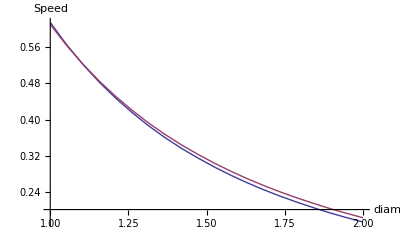

```mathematica
Plot[{SSpeed7[850,850,AM,.8,Rgal],SSpeed7[850,850,AM,.9,Rgal]},{AM,1,2}, PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,Speed},AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
STime7[λ_,λ0_,rapp_,Rg_]:=Sum[FAM[AM]/SSpeed7[λ,λ0,AM,rapp,Rg],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

```mathematica
STime7v3[λ_,λ0_,rapp_,Rg_,Vsig_]:=Sqrt[1+((rapp/1.57)/(2.355 Vsig/100))^2] Sum[FAM[AM]/SSpeed7[λ,λ0,AM,rapp,Rg],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

```mathematica
STime7v4[λ_,λ0_,rapp_,Rg_,Vsig_]:=Sqrt[1+((rapp/1.57)/(2.355 Vsig/75))^2] Sum[FAM[AM]/SSpeed7[λ,λ0,AM,rapp,Rg],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

```mathematica
SSpeed7ADC[λ_,AM_,rapp_,Rg_]:=ADCloss[λ] (AMloss[λ]^AM AppEffDR7[λ,λ,AM,rapp,Rg]/rapp)^2 /AM
```

```mathematica
STime7ADC[λ_,rapp_,Rg_]:=Sum[FAM[AM]/SSpeed7ADC[λ,AM,rapp,Rg],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

```mathematica
AppEffDR3[λ_,λ0_,AM_,rapp_,Rg_]:=AppEffd[Sqrt[MMEG2[Rsee[λ,AM],Rg,Ropt3[λ]]],BetaMEG0[Rsee[λ,AM],Rg,Ropt3[λ]],rapp,Sqrt[(10/56.73)^2+DR[λ,λ0,AM]^2]]
(* includes 10um decenering added in quadrature *)
```

```mathematica
SSpeed3ADC[λ_,AM_,rapp_,Rg_]:=ADCloss[λ](AMloss[λ]^AM AppEffDR3[λ,λ,AM,rapp,Rg]/rapp)^2 /AM
```

```mathematica
STime3ADC[λ_,rapp_,Rg_]:=Sum[FAM[AM]/SSpeed3ADC[λ,AM,rapp,Rg],{AM,{1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05}}]
```

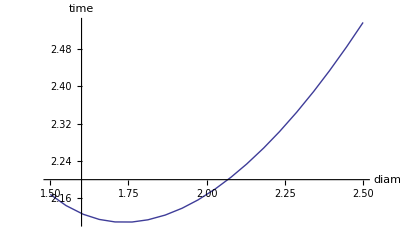

```mathematica
PT7Ng=Plot[STime7[850,850,dapp/2,Rgal],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

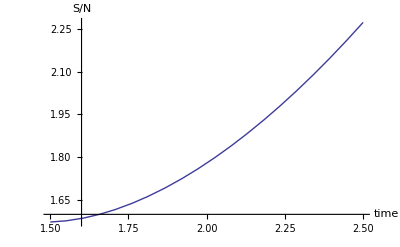

```mathematica
PT7Ngt=Plot[STime7[850,850,dapp/2,0],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {time,"S/N"},AxesStyle->Directive[Thick,14, Bold]]
```

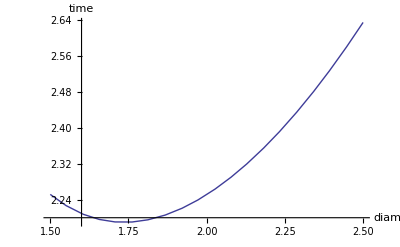

```mathematica
PT7Ag=Plot[STime7ADC[850,dapp/2,Rgal],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

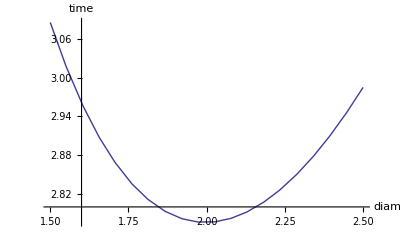

```mathematica
PT3Ag=Plot[STime3ADC[850,dapp/2,Rgal],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

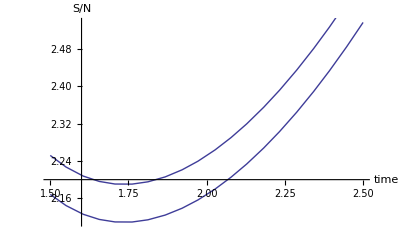

```mathematica
Show[PT7Ng,PT7Ag,AxesLabel->  {time,"S/N"},AxesStyle->Directive[Thick,14, Bold]]
```

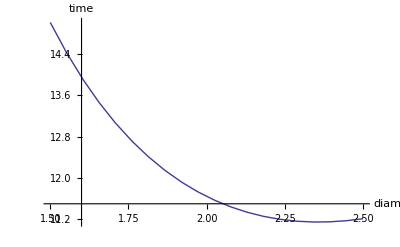

```mathematica
PT7Ns=Plot[STime7[350,425,dapp/2,0],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

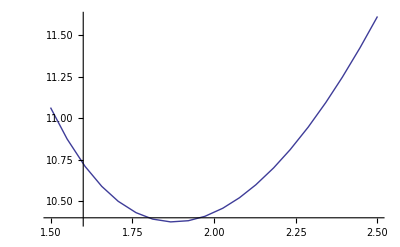

```mathematica
PT7As=Plot[STime7ADC[350,dapp/2,0],{dapp,1.5,2.5},PlotPoints->20,MaxRecursion->0]
```

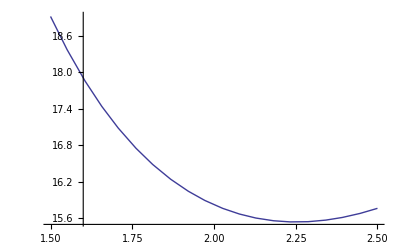

-Graphics-

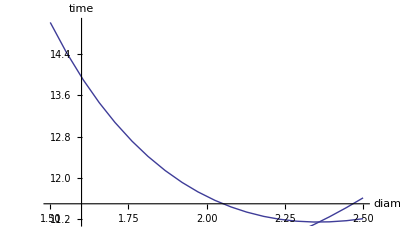

```mathematica
Show[PT7Ns,PT7As]
```

```mathematica
PT7Ngv=Plot[{STime7v[850,850,dapp/2,Rgal,40],STime7v[850,850,dapp/2,Rgal,80],STime7v[850,850,dapp/2,Rgal,120]},{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0]
```

-Graphics-

```mathematica
Plot[STime7v[850,850,dapp/2,Rgal,20],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0]
```

-Graphics-

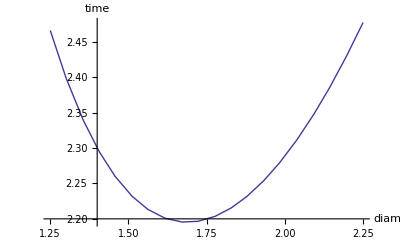

```mathematica
Plot[STime7v3[850,850,dapp/2,Rgal,80],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

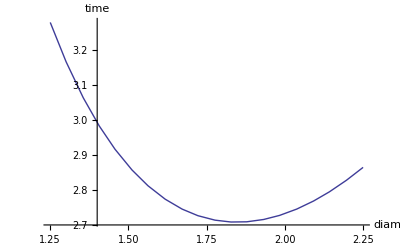

```mathematica
Plot[STime7v3[850,850,dapp/2,Rgalmax,80],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

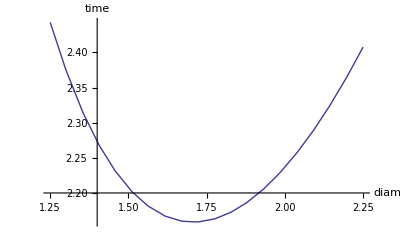

```mathematica
Plot[STime7v4[850,850,dapp/2,Rgal,80],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

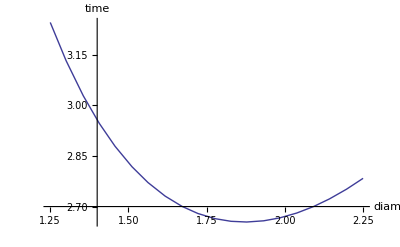

```mathematica
Plot[STime7v4[850,850,dapp/2,Rgalmax,80],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

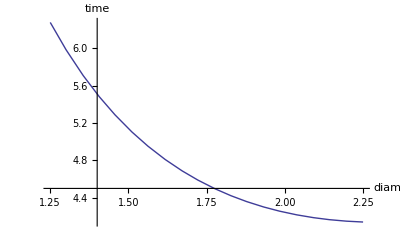

```mathematica
Plot[STime7v3[800,800,dapp/2,0.6667,300],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

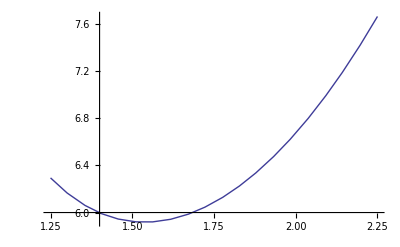

```mathematica
Plot[STime7v3[850,500,dapp/2,0,10],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0]
```

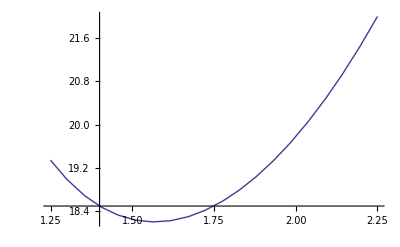

```mathematica
Plot[STime7v3[400,500,dapp/2,0,10],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0]
```

```mathematica
FindMinimum[STime7v[850,850,dapp/2,Rgal,40],{dapp,1.6}]
```

FindMinimum::nrnum: The function value STime7v[850, 850, 0.8, 0.29, 40] is not a real number at {dapp} = {1.6}.

FindMinimum[STime7v[850,850,dapp/2,Rgal,40],{dapp,1.6}]

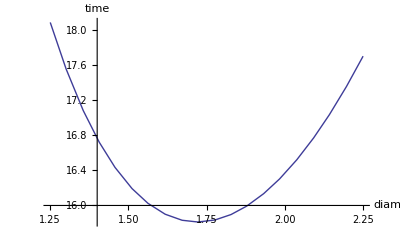

```mathematica
Plot[STime7v3[350,400,dapp/2,0,20],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

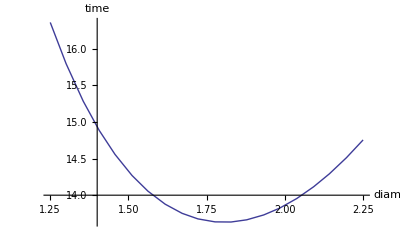

```mathematica
Plot[STime7v4[350,400,dapp/2,0,20],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

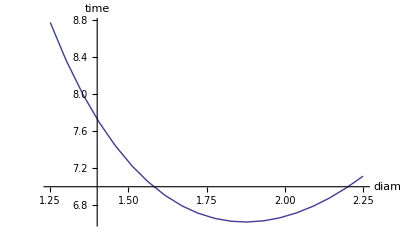

```mathematica
Plot[STime7v3[550,400,dapp/2,0,20],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0,PlotStyle->Thick,AxesLabel->  {diam,time},AxesStyle->Directive[Thick,14, Bold]]
```

```mathematica
FWHMsee500=0.9
```

0.9

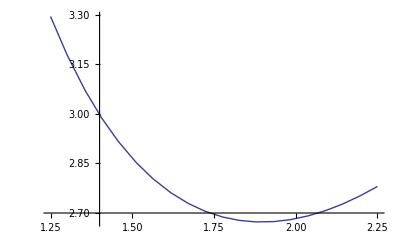

```mathematica
PT7As=Plot[STime7ADC[850,dapp/2,Rgal],{dapp,1.25,2.25},PlotPoints->20,MaxRecursion->0]
```

```mathematica
STime7ADC[850,1.45/2,Rgal]
```

2.92598

```mathematica
FWHMsee500=.75
```

0.75

```mathematica
STime7[850,850,1.57/2,Rgal]
```

2.13709

```mathematica
STime7[850,850,1.6/2,Rgal]
```

2.12746